## Plotting the

```mathematica
spin1={8.5,10.5,12.5,14.5,16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5,44.5,46.5,48.5};
spin2={13.5,15.5,17.5,19.5,21.5,23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5,43.5,45.5};
spin3={16.5,18.5,20.5,22.5,24.5,26.5,28.5,30.5,32.5,34.5,36.5,38.5,40.5,42.5};
spin4={23.5,25.5,27.5,29.5,31.5,33.5,35.5,37.5,39.5,41.5};
tsd1={0.1966,0.4597,0.7746,1.1609,1.6112,2.1265,2.7051,3.3441,4.0411,4.7937,5.5992,6.457,7.3667,8.3293,9.3458,10.4169,11.5431,12.7224,13.9491,15.2181,16.5221};
tsd2={1.3394,1.7467,2.2184,2.7527,3.3484,4.003,4.7143,5.4805,6.3004,7.1733,8.0998,9.08,10.1147,11.2036,12.3466,13.5441,14.7911};
tsd3={2.1237,2.6293,3.1973,3.8243,4.5094,5.2506,6.0465,6.8963,7.7988,8.7546,9.7638,10.8268,11.9392,13.0861};
tsd4={4.58,5.2251,5.9273,6.6819,7.4919,8.3573,9.2778,10.2535,11.2851,12.3701};
thData={0.324218,0.691218,1.10213,1.55761,2.0581,2.60389,3.19519,3.83213,4.5148,5.24328,6.01757,6.83768,7.70356,8.61514,9.57231,10.5749,11.6226,12.715,13.8515,15.031,16.2513,1.58191,2.06141,2.581,3.14156,3.7437,4.38784,5.07426,5.80313,6.57452,7.38841,8.24467,9.14309,10.0833,11.0647,12.0866,13.1477,14.2461,2.56521,3.1039,3.67923,4.29222,4.94356,5.63372,6.36298,7.13147,7.93913,8.78578,9.67103,10.5943,11.5546,12.5507,4.16774,4.87331,5.6247,6.4219,7.2649,8.15365,9.08804,10.0679,11.0931,12.1632};
(*best results obtain on 14hr simulation @ELK VM*)
(*thData={0.278938,0.607212,0.985682,1.41486,1.8951,2.42663,3.00963,3.64423,4.33055,5.06867,5.85866,6.70059,7.59449,8.54043,9.53842,10.5885,11.6907,12.8451,14.0516,15.3104,16.6213,1.35772,1.81252,2.31575,2.8681,3.47009,4.12211,4.82448,5.57744,6.3812,7.23591,8.14171,9.09874,10.1071,11.1668,12.2781,13.4408,14.6552,2.21019,2.7364,3.30957,3.93055,4.6,5.31842,6.08622,6.90373,7.77123,8.68894,9.65705,10.6757,11.7451,12.8654,3.98092,4.69313,5.45718,6.27313,7.14104,8.06095,9.03291,10.057,11.1331,12.2614};*)
tsd1th=Table[thData[[i]],{i,1,21}];
tsd2th=Table[thData[[i]],{i,22,38}];
tsd3th=Table[thData[[i]],{i,39,52}];
tsd4th=Table[thData[[i]],{i,53,62}];
expData=Join[tsd1,tsd2,tsd3,tsd4];
n1=21;
n2=17;
n3=14;
n4=10;
data1exp=Table[{spin1[[i]],tsd1[[i]]},{i,1,Length[tsd1]}];
data2exp=Table[{spin2[[i]],tsd2[[i]]},{i,1,Length[tsd2]}];
data3exp=Table[{spin3[[i]],tsd3[[i]]},{i,1,Length[tsd3]}];
data4exp=Table[{spin4[[i]],tsd4[[i]]},{i,1,Length[tsd4]}];
data1th=Table[{spin1[[i]],tsd1th[[i]]},{i,1,Length[tsd1th]}];
data2th=Table[{spin2[[i]],tsd2th[[i]]},{i,1,Length[tsd2th]}];
data3th=Table[{spin3[[i]],tsd3th[[i]]},{i,1,Length[tsd3th]}];
data4th=Table[{spin4[[i]],tsd4th[[i]]},{i,1,Length[tsd4th]}];
SPINS=Join[spin1,spin2,spin3,spin4];
```

```mathematica
RMS[exp_,th_]:=Sqrt[Sum[(exp[[i]]-th[[i]])^2,{i,1,Length[exp]}]/(Length[exp]+1)];
```

```mathematica
RMS[expData,thData]
```

0.217947

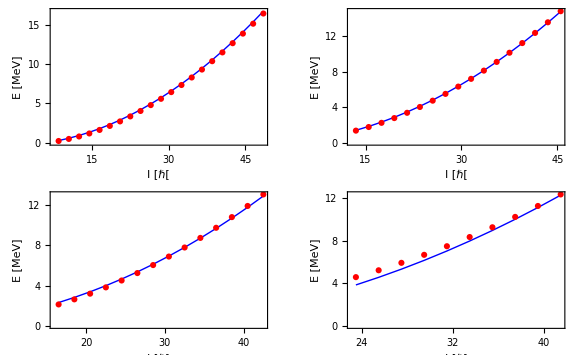

```mathematica
p1[exp_,th_]:=ListPlot[{exp,th},Frame->True,Axes->False,Joined->{False,True},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic,None},FrameLabel->{"I [ℏ[","E [MeV]"},LabelStyle->{14,Bold,Black,FontFamily->"Times New Roman"}];
GraphicsGrid[{{p1[data1exp,data1th],p1[data2exp,data2th]}, 
 {p1[data3exp,data3th],p1[data4exp,data4th]}},Frame->None,ImageSize->Large]
```